# Neutral Site Analysis

### Using Mathematica to investigate variations in samples from Porto

## Header

### Standard Header Section

```mathematica
Needs["HierarchicalClustering`"]
Needs["ProteomicsAnalysis`"]
Needs["ManualPCA`"]
Needs["PrincipalComponentsVariance`"]
Needs["VennDiagram`"]
Needs["Sanitized`"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\cygwin64\home\Andrew\Dropbox\shared_AL\Porto_iTRAQ_neutral-sites

```mathematica
FileNames[]
```

{13211_iTRAQ2-pepts.xls,13211_iTRAQ2-quants.xls,13212_iTRAQ1-pepts.xls,13212_iTRAQ1-PHENYX.xls,13212_iTRAQ1-quants.xls,GFP_analysis.r,GFP_measurements.csv,GFP_measurementsRAW-iTRAQ_samples.xlsx,GFP_measurements.xlsx,.git,neutral_sites_investigation.nb,porto_iTRAQ1-EASYPROT.xlsx,porto_iTRAQ1_peptide-data.csv,Porto_PCA_iTRAQ1.pdf,Porto_PCA_iTRAQ2.pdf,ProteomicsAnalysis.m,README.md,Report.nb,Report.pdf,SignifiQuant_WTvs10G.xls,SignifiQuant_WTvs15B.xls,SignifiQuant_WTvs15G.xls,SignifiQuant_WTvs16G.xls,SignifiQuant_WTvs5G.xls,SignifiQuant_WTvs8G.xls}

## Protein investigation

### Import data

```mathematica
proteins1=Import["13212_iTRAQ1-quants.xls"][[2]];
proteins2=Import["13211_iTRAQ2-quants.xls"][[2]];
proteins1//Dimensions
proteins2//Dimensions
```

{464,66}

{631,66}

### Collect intersecting proteins

```mathematica
acValues1=proteins1[[3;;All,1]];
acValues2=proteins2[[3;;All,1]];
```

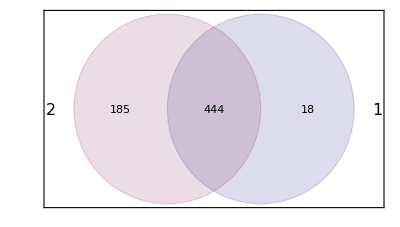

```mathematica
VennDiagram[{acValues1,acValues2}]
```

```mathematica
sharedProteins=Intersection[acValues1,acValues2];
Dimensions[sharedProteins]
```

{444}

### PCA of intersecting proteins

```mathematica
proteinIntensities1=Map[Association@@Thread[acValues1->#]&,proteins1[[3;;All,27;;34]]ᵀ]; (*Isotopic correction, Median correction, Log Values*)
proteinIntensities2=Map[Association@@Thread[acValues2->#]&,proteins2[[3;;All,27;;34]]ᵀ];
```

```mathematica
sharedProteinIntensities=Table[f[[All,Key[sharedProteins[[k]]]]],{k,Length[sharedProteins]},{f,{proteinIntensities1,proteinIntensities2}}];
sharedProteinIntensities=Flatten[Transpose[sharedProteinIntensities,{3,1,2}],1]ᵀ;
```

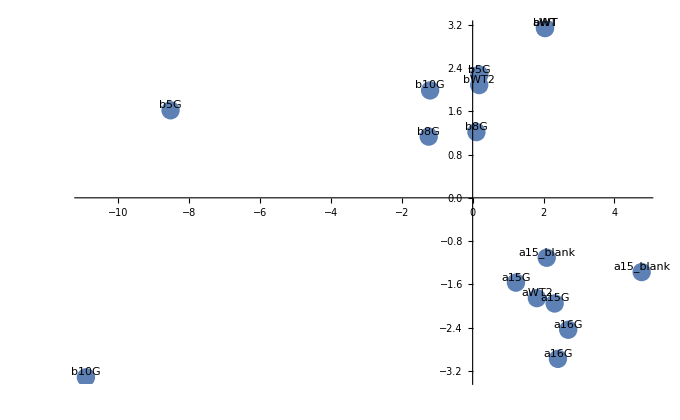

```mathematica
labels={"aWT","aWT2","a15G","a15G","a16G","a16G","a15_blank","a15_blank","bWT","bWT2","b5G","b5G","b8G","b8G","b10G","b10G"};
pca=PrincipalComponents[sharedProteinIntensitiesᵀ];
ListPlot[pca[[All,1;;2]],Epilog->Table[Text[labels[[i]],pca[[i,{1,2}]],{0,-2}],{i,16}],PlotRangePadding->Scaled[.1],PlotRange->Full]
```

Not meshing properly based on WT2 positioning.

## Peptide investigation

### Import data

```mathematica
rawPeptideData1=Import["13212_iTRAQ1-pepts.xls"][[1]];
rawPeptideData2=Import["13211_iTRAQ2-pepts.xls"][[1]];
Dimensions[rawPeptideData1]
Dimensions[rawPeptideData2]
```

{8000,20}

{14815,20}

### Putting the data into a workable format

```mathematica
heads=rawPeptideData1[[1,All]];
workingPeptideData1=rawPeptideData1[[2;;All,All]];
workingPeptideData2=rawPeptideData2[[2;;All,All]];
```

```mathematica
heads[[11;;18]]
labelIntensities1=workingPeptideData1[[All,11;;18]];
labelIntensities2=workingPeptideData2[[All,11;;18]];
```

{113.1,114.1,115.1,116.1,117.1,118.1,119.1,121.1}

```mathematica
{proteinLabels1,proteinLabels2}={workingPeptideData1[[All,{2,3}]],workingPeptideData2[[All,{2,3}]]};
```

```mathematica
Union[proteinLabels1[[All,1]],proteinLabels2[[All,1]]]//Length
```

749

### Removing null intensity data

```mathematica
labelIntensities1=labelIntensities1/.""->0.;
labelIntensities2=labelIntensities2/.""->0.;
```

```mathematica
labelIntensities1=Join[proteinLabels1ᵀ,labelIntensities1ᵀ]ᵀ;
labelIntensities2=Join[proteinLabels2ᵀ,labelIntensities2ᵀ]ᵀ;
```

```mathematica
labelIntensities1[[1]]
```

{M1LID4,SALDEIVLVGGSTR,0.5546,0.5856,0.5499,0.8452,0.791,0.6297,0.6373,0.6327}

```mathematica
Table[MemberQ[i,0.],{i,labelIntensities1}]//Tally
```

{{False,6934},{True,1065}}

#### **OPTIONAL - remove any rows containing 0 intensity anywhere.**

```mathematica
(*labelIntensities1=Pick[labelIntensities1,#,False]&[Table[MemberQ[i,0.],{i,labelIntensities1}]];
labelIntensities2=Pick[labelIntensities2,#,False]&[Table[MemberQ[i,0.],{i,labelIntensities2}]];*)
```

### Mapping associations

```mathematica
labelIntensities1=Map[AssociationThread[heads[[11;;18]]->#]&,labelIntensities1[[All,3;;All]]];
labelIntensities2=Map[AssociationThread[heads[[11;;18]]->#]&,labelIntensities2[[All,3;;All]]];
c1=labelIntensities1;
c2=labelIntensities2;(*For comparison*)
```

### Normalising the data

#### By channel sum

```mathematica
a1=Table[
(100000/Total[#[[All,i]]])*#[[All,i]],{i,8}]ᵀ;&[labelIntensities1]
a1=Map[AssociationThread[heads[[11;;18]]->#]&,a1];

a2=Table[
(100000/Total[#[[All,i]]])*#[[All,i]],{i,8}]ᵀ;&[labelIntensities2]
a2=Map[AssociationThread[heads[[11;;18]]->#]&,a2];
```

```mathematica
a1[[1]]
```

<|113.1→8.06501,114.1→9.5593,115.1→9.71687,116.1→12.3677,117.1→11.8442,118.1→11.9918,119.1→11.0602,121.1→11.7583|>

```mathematica
Length[a1]
```

7999

#### By median correction

This should be a function, it’s failing for arbitrary reasons. Doesn’t like the loop for determining the quartiles for some reasons.

```mathematica
(*
medianCorrection[data_]:=Association@@Table[
log=Log[data⟦All,Key[k]⟧];
p=Flatten[Position[log,Indeterminate]];
min=Sanitized[Min][N[log]];
log=N[log]/.Indeterminate->min;
log=N[log]/.-∞->min;
{L,M,R}=Evaluate[Quantile[log,{0.4,0.5,0.6}]];
n=(log-M)/(R-L);
n⟦p⟧=-∞;
k->n,
{k,heads[[11;;18]]}]
*)
```

```mathematica
b1=c1;
normalised=Association@@Table[
log=Log[#⟦All,Key[k]⟧];
p=Flatten[Position[log,Indeterminate]];
min=Sanitized[Min][N[log]];
log=N[log]/.Indeterminate->min;
{L,M,R}=Quantile[log,{0.4,0.5,0.6}];
n=(log-M)/(R-L);
n⟦p⟧=-∞;
k->n,
{k,heads[[11;;18]]}];&[b1]
Do[b1⟦All,Key[k]⟧=Exp[normalised⟦Key[k]⟧],{k,heads[[11;;18]]}]
```

```mathematica
b2=c2;
normalised=Association@@Table[
log=Log[#⟦All,Key[k]⟧];
p=Flatten[Position[log,Indeterminate]];
min=Sanitized[Min][N[log]];
log=N[log]/.Indeterminate->min;
{L,M,R}=Quantile[log,{0.4,0.5,0.6}];
n=(log-M)/(R-L);
n⟦p⟧=-∞;
k->n,
{k,heads[[11;;18]]}];&[b2]
Do[b2⟦All,Key[k]⟧=Exp[normalised⟦Key[k]⟧],{k,heads[[11;;18]]}]
```

#### Graphs

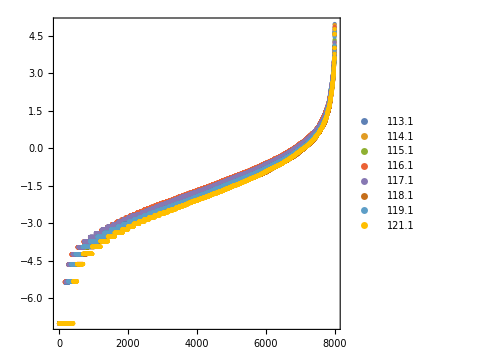
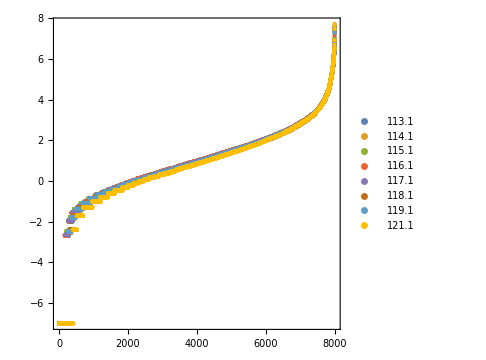
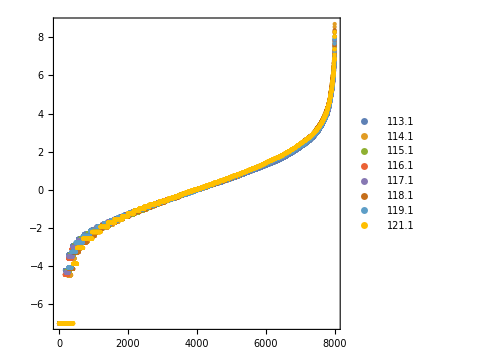
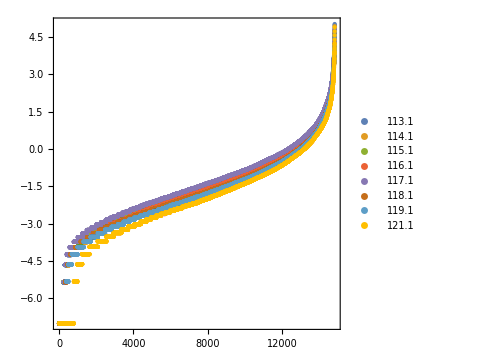
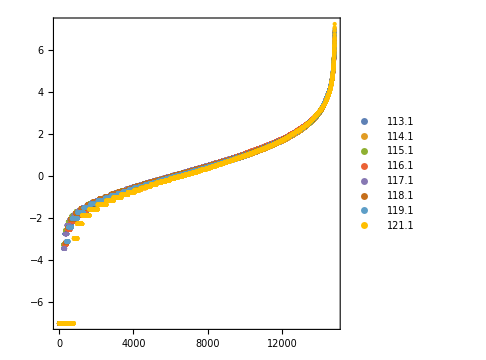
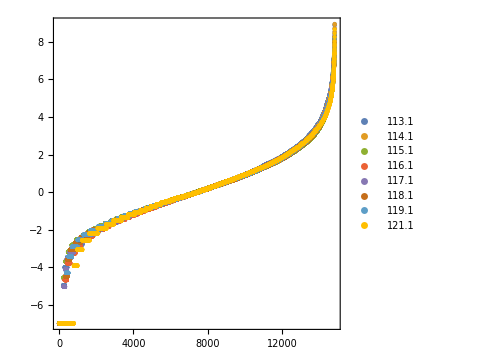

```mathematica
graphs=Table[ListPlot[Evaluate@Table[Sort[N[Log[#⟦All,Key[k]⟧/.(0|0.->Exp[-7.])]]],{k,heads[[11;;18]]}],
PlotRange->All,Frame->True,AspectRatio->1,ImageSize->Medium,
PlotLegends->heads[[11;;18]],PlotStyle->PointSize[Medium]]&[i],{i,{c1,a1,b1,c2,a2,b2}}]
```

### Looking at GFP

#### *** Look at the channel sum for GFP vs the channel sum for the whole label

```mathematica
{normalisedPeptideData1,normalisedPeptideData2}={workingPeptideData1,workingPeptideData2};
{normalisedPeptideData1[[All,11;;18]],normalisedPeptideData2[[All,11;;18]]}={Values@b1,Values@b2};
```

```mathematica
Pick[normalisedPeptideData1,#]&[Table[normalisedPeptideData1[[i,2]]=="P42212",{i,Length[normalisedPeptideData1]}]]//TableForm
```

13212. | P42212 | SAMPEGYVQER | 2. | 10.4924 | 4.306×10^-24 | 1. | 785.899 | 0. | iTRAQ_8plex_Nterm:::::::::::: | 0.249111 | 1.15753 | 97.096 | 86.0472 | 75.8985 | 93.5064 | 0 | 0.455312 | File: FIL_ITRAQ1_F72.wiff, Sample: FIL_ITRAQ1_F72 (sample number 1), Elution: 47.522 to 49.719 min, Period: 1, Cycle(s): 2566, 2575 (Experiment 2), 2584 (Experiment 3) | SAMPEGYVQER%iTRAQ_8plex_Nterm::::::::::::%sample_0%cmpd_27482
13212. | P42212 | FEGDTLVNR | 2. | 9.55749 | 4.886×10^-20 | 1. | 677.869 | 0. | iTRAQ_8plex_Nterm:::::::::: | 0.531658 | 1. | 14.5297 | 13.7948 | 18.0981 | 22.7659 | 0 | 0.540828 | File: FIL_ITRAQ1_F57.wiff, Sample: FIL_ITRAQ1_F57 (sample number 1), Elution: 52.826 to 53.898 min, Period: 1, Cycle(s): 2413, 2422 (Experiment 2) | FEGDTLVNR%iTRAQ_8plex_Nterm::::::::::%sample_0%cmpd_14367
13212. | P42212 | FEGDTLVNR | 2. | 8.1352 | 1.624×10^-14 | 1. | 677.857 | 0. | iTRAQ_8plex_Nterm:::::::::: | 3.94006 | 1.36168 | 56.8683 | 54.142 | 64.8045 | 74.9006 | 0 | 1.65643 | File: FIL_ITRAQ1_F57_02.wiff, Sample: FIL_ITRAQ1_F57_02 (sample number 1), Elution: 52.637 to 53.71 min, Period: 1, Cycle(s): 2384, 2393 (Experiment 2) | FEGDTLVNR%iTRAQ_8plex_Nterm::::::::::%sample_0%cmpd_9571
13212. | P42212 | SAMPEGYVQER | 2. | 8.68045 | 1.813×10^-16 | 1. | 785.899 | 0. | iTRAQ_8plex_Nterm:::::::::::: | 0.0339118 | 0.0114515 | 3.14279 | 2.51959 | 2.50279 | 1.89657 | 0 | 0 | File: FIL_ITRAQ1_F73.wiff, Sample: FIL_ITRAQ1_F73 (sample number 1), Elution: 47.82 min, Period: 1, Cycle(s): 2605 (Experiment 3) | SAMPEGYVQER%iTRAQ_8plex_Nterm::::::::::::%sample_0%cmpd_1131
13212. | P42212 | QHDFFK | 2. | 5.24708 | 7.572×10^-6 | 1. | 715.425 | 0. | iTRAQ_8plex_Nterm::::::iTRAQ_8plex_K: | 0.0543118 | 0.112734 | 5.75371 | 5.39044 | 4.6204 | 6.34886 | 0 | 0.0776986 | File: FIL_ITRAQ1_F64_02.wiff, Sample: FIL_ITRAQ1_F64_02 (sample number 1), Elution: 46.746 min, Period: 1, Cycle(s): 2563 (Experiment 2) | QHDFFK%iTRAQ_8plex_Nterm::::::iTRAQ_8plex_K:%sample_0%cmpd_20158
13212. | P42212 | FICTTGK | 2. | 5.20107 | 8.025×10^-6 | 1. | 712.401 | 0. | iTRAQ_8plex_Nterm:::MMTS::::iTRAQ_8plex_K: | 0.30313 | 0.244908 | 9.60777 | 9.49111 | 7.9622 | 11.0024 | 0 | 0.253226 | File: FIL_ITRAQ1_F69_02.wiff, Sample: FIL_ITRAQ1_F69_02 (sample number 1), Elution: 59.922 min, Period: 1, Cycle(s): 2860 (Experiment 2) | FICTTGK%iTRAQ_8plex_Nterm:::MMTS::::iTRAQ_8plex_K:%sample_0%cmpd_22256
13212. | P42212 | FICTTGK | 3. | 7.55236 | 2.736×10^-12 | 1. | 475.268 | 0. | iTRAQ_8plex_Nterm:::MMTS::::iTRAQ_8plex_K: | 0.0543118 | 0 | 0.80398 | 0.719053 | 0.738338 | 0.773879 | 0 | 0.179067 | File: FIL_ITRAQ1_F68_02.wiff, Sample: FIL_ITRAQ1_F68_02 (sample number 1), Elution: 59.908 min, Period: 1, Cycle(s): 2726 (Experiment 2) | FICTTGK%iTRAQ_8plex_Nterm:::MMTS::::iTRAQ_8plex_K:%sample_0%cmpd_22707
13212. | P42212 | FICTTGK | 3. | 6.8712 | 4.074×10^-10 | 1. | 475.277 | 0. | iTRAQ_8plex_Nterm:::MMTS::::iTRAQ_8plex_K: | 0.0543118 | 0 | 0.921097 | 0.347552 | 0.319985 | 0.729571 | 0.0892683 | 0.0476765 | File: FIL_ITRAQ1_F69_02.wiff, Sample: FIL_ITRAQ1_F69_02 (sample number 1), Elution: 59.99 min, Period: 1, Cycle(s): 2861 (Experiment 2) | FICTTGK%iTRAQ_8plex_Nterm:::MMTS::::iTRAQ_8plex_K:%sample_0%cmpd_22257
13212. | P42212 | FICTTGK | 3. | 5.73866 | 6.107×10^-7 | 1. | 475.277 | 0. | iTRAQ_8plex_Nterm:::MMTS::::iTRAQ_8plex_K: | 0.249111 | 0.216541 | 0.881716 | 1.09717 | 0.738998 | 0.64346 | 0.2672 | 0.0776986 | File: FIL_ITRAQ1_F68_02.wiff, Sample: FIL_ITRAQ1_F68_02 (sample number 1), Elution: 58.971 min, Period: 1, Cycle(s): 2707 (Experiment 3) | FICTTGK%iTRAQ_8plex_Nterm:::MMTS::::iTRAQ_8plex_K:%sample_0%cmpd_22693
13212. | P42212 | EDGNILGHK | 3. | 5.92223 | 1.937×10^-7 | 1. | 530.957 | 0. | iTRAQ_8plex_Nterm:::::::::iTRAQ_8plex_K: | 0.146922 | 0.162801 | 0.372789 | 0.599954 | 0.93368 | 1.94904 | 0 | 0.0476765 | File: FIL_ITRAQ1_F47_02.wiff, Sample: FIL_ITRAQ1_F47_02 (sample number 1), Elution: 45.14 min, Period: 1, Cycle(s): 2313 (Experiment 2) | EDGNILGHK%iTRAQ_8plex_Nterm:::::::::iTRAQ_8plex_K:%sample_0%cmpd_2780
13212. | P42212 | GIDFKEDGNILGHK | 3. | 6.83499 | 5.987×10^-10 | 1. | 819.127 | 1. | iTRAQ_8plex_Nterm:::::iTRAQ_8plex_K:::::::::iTRAQ_8plex_K: | 4.30096 | 3.66812 | 38.7593 | 36.4805 | 34.6979 | 40.42 | 0 | 1.60412 | File: FIL_ITRAQ1_F74.wiff, Sample: FIL_ITRAQ1_F74 (sample number 1), Elution: 56.88 to 57.833 min, Period: 1, Cycle(s): 2750 (Experiment 2), 2758 (Experiment 3) | GIDFKEDGNILGHK%iTRAQ_8plex_Nterm:::::iTRAQ_8plex_K:::::::::iTRAQ_8plex_K:%sample_0%cmpd_701

```mathematica
Pick[normalisedPeptideData2,#]&[Table[normalisedPeptideData2[[i,2]]=="P42212",{i,Length[normalisedPeptideData2]}]]//TableForm
```

13211. | P42212 | FSVSGEGEGDATYGK | 3. | 13.3375 | 7.567×10^-39 | 1. | 704.666 | 0. | iTRAQ_8plex_Nterm:::::::::::::::iTRAQ_8plex_K: | 0.292239 | 0.128615 | 8.76266 | 5.93813 | 9.62187 | 8.12393 | 9.64525 | 2.97 | File: FIL2_ITRAQ2_F77.wiff, Sample: FIL2_ITRAQ2_F77 (sample number 1), Elution: 55.416 min, Period: 1, Cycle(s): 2905 (Experiment 2) | FSVSGEGEGDATYGK%iTRAQ_8plex_Nterm:::::::::::::::iTRAQ_8plex_K:%sample_0%cmpd_32863
13211. | P42212 | SAMPEGYVQER | 2. | 10.4455 | 6.608×10^-24 | 1. | 785.924 | 0. | iTRAQ_8plex_Nterm:::::::::::: | 1.0334 | 1.87068 | 213.079 | 181.431 | 221.168 | 167.086 | 197.55 | 48.0313 | File: FIL2_ITRAQ2_F72.wiff, Sample: FIL2_ITRAQ2_F72 (sample number 1), Elution: 48.368 to 50.565 min, Period: 1, Cycle(s): 2653, 2662 (Experiment 2), 2671 (Experiment 3) | SAMPEGYVQER%iTRAQ_8plex_Nterm::::::::::::%sample_0%cmpd_30296
13211. | P42212 | FEGDTLVNR | 2. | 9.00664 | 8.924×10^-18 | 1. | 677.857 | 0. | iTRAQ_8plex_Nterm:::::::::: | 0.933351 | 2.15602 | 65.9937 | 46.681 | 66.3263 | 51.9312 | 59.793 | 19.0736 | File: FIL2_ITRAQ2_F57_02.wiff, Sample: FIL2_ITRAQ2_F57_02 (sample number 1), Elution: 55.013 to 56.087 min, Period: 1, Cycle(s): 2527, 2536 (Experiment 2) | FEGDTLVNR%iTRAQ_8plex_Nterm::::::::::%sample_0%cmpd_17725
13211. | P42212 | FEGDTLVNR | 2. | 8.52905 | 6.419×10^-16 | 1. | 677.869 | 0. | iTRAQ_8plex_Nterm:::::::::: | 3.51171 | 4.7951 | 97.1031 | 65.1152 | 105.139 | 86.5158 | 85.5517 | 32.0415 | File: FIL2_ITRAQ2_F57.wiff, Sample: FIL2_ITRAQ2_F57 (sample number 1), Elution: 54.379 to 56.526 min, Period: 1, Cycle(s): 2508 (Experiment 2), 2499, 2517 (Experiment 3) | FEGDTLVNR%iTRAQ_8plex_Nterm::::::::::%sample_0%cmpd_17271
13211. | P42212 | FSVSGEGEGDATYGK | 3. | 11.4469 | 1.316×10^-28 | 1. | 704.678 | 0. | iTRAQ_8plex_Nterm:::::::::::::::iTRAQ_8plex_K: | 0.135303 | 0.515706 | 1.31763 | 1.79169 | 2.2129 | 1.61744 | 2.82415 | 0.898326 | File: FIL2_ITRAQ2_F77.wiff, Sample: FIL2_ITRAQ2_F77 (sample number 1), Elution: 56.847 min, Period: 1, Cycle(s): 2917 (Experiment 2) | FSVSGEGEGDATYGK%iTRAQ_8plex_Nterm:::::::::::::::iTRAQ_8plex_K:%sample_0%cmpd_32877
13211. | P42212 | SAMPEGYVQER | 2. | 8.82844 | 4.564×10^-17 | 1. | 785.924 | 0. | iTRAQ_8plex_Nterm:::::::::::: | 0.045649 | 0.128615 | 1.20997 | 2.03664 | 2.72596 | 2.67204 | 3.19862 | 1.10367 | File: FIL2_ITRAQ2_F73.wiff, Sample: FIL2_ITRAQ2_F73 (sample number 1), Elution: 48.712 min, Period: 1, Cycle(s): 2697 (Experiment 2) | SAMPEGYVQER%iTRAQ_8plex_Nterm::::::::::::%sample_0%cmpd_30762
13211. | P42212 | QHDFFK | 2. | 5.48525 | 1.837×10^-6 | 1. | 715.401 | 0. | iTRAQ_8plex_Nterm::::::iTRAQ_8plex_K: | 0.0965299 | 0.321565 | 10.1945 | 6.90599 | 11.5584 | 8.80848 | 9.64525 | 2.78189 | File: FIL2_ITRAQ2_F63_02.wiff, Sample: FIL2_ITRAQ2_F63_02 (sample number 1), Elution: 47.523 to 48.477 min, Period: 1, Cycle(s): 2630 (Experiment 2), 2619 (Experiment 3) | QHDFFK%iTRAQ_8plex_Nterm::::::iTRAQ_8plex_K:%sample_0%cmpd_23218
13211. | P42212 | AEVKFEGDTLVNR | 3. | 8.77819 | 1.08×10^-16 | 1. | 696.068 | 1. | iTRAQ_8plex_Nterm::::iTRAQ_8plex_K:::::::::: | 0.115297 | 0.0244987 | 4.82296 | 3.68079 | 4.92003 | 4.6845 | 3.1442 | 1.10367 | File: FIL2_ITRAQ2_F65_02.wiff, Sample: FIL2_ITRAQ2_F65_02 (sample number 1), Elution: 56.421 min, Period: 1, Cycle(s): 2748 (Experiment 3) | AEVKFEGDTLVNR%iTRAQ_8plex_Nterm::::iTRAQ_8plex_K::::::::::%sample_0%cmpd_25040
13211. | P42212 | SAMPEGYVQER | 2. | 7.26746 | 1.575×10^-11 | 1. | 785.924 | 0. | iTRAQ_8plex_Nterm:::::::::::: | 0.135303 | 0.0612521 | 1.53933 | 1.17871 | 1.08936 | 1.79251 | 0.793623 | 0.109597 | File: FIL2_ITRAQ2_F72.wiff, Sample: FIL2_ITRAQ2_F72 (sample number 1), Elution: 51.894 min, Period: 1, Cycle(s): 2683 (Experiment 2) | SAMPEGYVQER%iTRAQ_8plex_Nterm::::::::::::%sample_0%cmpd_30314
13211. | P42212 | SAMPEGYVQER | 2. | 7.44701 | 3.915×10^-12 | 1. | 785.936 | 0. | iTRAQ_8plex_Nterm:::::::::::: | 0.0965299 | 0.2342 | 0.54756 | 1. | 1. | 0.526504 | 1.30536 | 0.425769 | File: FIL2_ITRAQ2_F71.wiff, Sample: FIL2_ITRAQ2_F71 (sample number 1), Elution: 49.275 min, Period: 1, Cycle(s): 2613 (Experiment 2) | SAMPEGYVQER%iTRAQ_8plex_Nterm::::::::::::%sample_0%cmpd_29744
13211. | P42212 | QHDFFK | 2. | 5.69218 | 5.393×10^-7 | 1. | 715.389 | 0. | iTRAQ_8plex_Nterm::::::iTRAQ_8plex_K: | 0.0308845 | 0.0244987 | 3.66196 | 2.41564 | 4.70431 | 4.19871 | 4.37573 | 0.749869 | File: FIL2_ITRAQ2_F64.wiff, Sample: FIL2_ITRAQ2_F64 (sample number 1), Elution: 49.086 to 50.107 min, Period: 1, Cycle(s): 2749, 2758 (Experiment 2) | QHDFFK%iTRAQ_8plex_Nterm::::::iTRAQ_8plex_K:%sample_0%cmpd_23661
13211. | P42212 | FSVSGEGEGDATYGK | 3. | 9.38206 | 3.493×10^-19 | 1. | 704.666 | 0. | iTRAQ_8plex_Nterm:::::::::::::::iTRAQ_8plex_K: | 0.560762 | 0.2342 | 0.86516 | 1.0352 | 1.96617 | 1.53142 | 1. | 0.898326 | File: FIL2_ITRAQ2_F77.wiff, Sample: FIL2_ITRAQ2_F77 (sample number 1), Elution: 58.874 min, Period: 1, Cycle(s): 2934 (Experiment 2) | FSVSGEGEGDATYGK%iTRAQ_8plex_Nterm:::::::::::::::iTRAQ_8plex_K:%sample_0%cmpd_32900
13211. | P42212 | FICTTGK | 3. | 7.79346 | 3.879×10^-13 | 1. | 475.268 | 0. | iTRAQ_8plex_Nterm:::MMTS::::iTRAQ_8plex_K: | 0.0965299 | 0.29191 | 12.4827 | 5.72794 | 12.9142 | 10.5379 | 12.5296 | 4.68922 | File: FIL2_ITRAQ2_F68_02.wiff, Sample: FIL2_ITRAQ2_F68_02 (sample number 1), Elution: 60.625 to 61.597 min, Period: 1, Cycle(s): 2792 (Experiment 2), 2783 (Experiment 3) | FICTTGK%iTRAQ_8plex_Nterm:::MMTS::::iTRAQ_8plex_K:%sample_0%cmpd_27517
13211. | P42212 | FICTTGK | 3. | 7.75555 | 5.234×10^-13 | 1. | 475.258 | 0. | iTRAQ_8plex_Nterm:::MMTS::::iTRAQ_8plex_K: | 0.045649 | 0.10518 | 0.798989 | 0.136916 | 1.43169 | 0.773524 | 0.560146 | 0.109597 | File: FIL2_ITRAQ2_F69_02.wiff, Sample: FIL2_ITRAQ2_F69_02 (sample number 1), Elution: 61.623 to 62.713 min, Period: 1, Cycle(s): 2750, 2760 (Experiment 3) | FICTTGK%iTRAQ_8plex_Nterm:::MMTS::::iTRAQ_8plex_K:%sample_0%cmpd_28498
13211. | P42212 | FSVSGEGEGDATYGK | 2. | 7.40143 | 4.917×10^-12 | 1. | 1056.51 | 0. | iTRAQ_8plex_Nterm:::::::::::::::iTRAQ_8plex_K: | 0.00700522 | 0 | 3.57171 | 1.63305 | 2.46579 | 1. | 3.25322 | 0.109597 | File: FIL2_ITRAQ2_F77.wiff, Sample: FIL2_ITRAQ2_F77 (sample number 1), Elution: 54.871 min, Period: 1, Cycle(s): 2900 (Experiment 2) | FSVSGEGEGDATYGK%iTRAQ_8plex_Nterm:::::::::::::::iTRAQ_8plex_K:%sample_0%cmpd_32855
13211. | P42212 | FICTTGK | 3. | 7.64479 | 1.245×10^-12 | 1. | 475.268 | 0. | iTRAQ_8plex_Nterm:::MMTS::::iTRAQ_8plex_K: | 0.0614096 | 0.128615 | 2.74284 | 1.32635 | 1.14954 | 1.88058 | 2.15785 | 0.898326 | File: FIL2_ITRAQ2_F69.wiff, Sample: FIL2_ITRAQ2_F69 (sample number 1), Elution: 61.281 to 62.456 min, Period: 1, Cycle(s): 2733 (Experiment 2), 2742 (Experiment 3) | FICTTGK%iTRAQ_8plex_Nterm:::MMTS::::iTRAQ_8plex_K:%sample_0%cmpd_27986
13211. | P42212 | TIFFKDDGNYK | 3. | 8.4387 | 2.054×10^-15 | 1. | 754.092 | 1. | iTRAQ_8plex_Nterm:::::iTRAQ_8plex_K::::::iTRAQ_8plex_K: | 0.0614096 | 0.0612521 | 5.4526 | 4.06341 | 5.98828 | 3.98639 | 5.08255 | 1.37195 | File: FIL2_ITRAQ2_F90.wiff, Sample: FIL2_ITRAQ2_F90 (sample number 1), Elution: 62.906 min, Period: 1, Cycle(s): 3498 (Experiment 2) | TIFFKDDGNYK%iTRAQ_8plex_Nterm:::::iTRAQ_8plex_K::::::iTRAQ_8plex_K:%sample_0%cmpd_38813
13211. | P42212 | FICTTGK | 2. | 5.44727 | 1.918×10^-6 | 1. | 712.401 | 0. | iTRAQ_8plex_Nterm:::MMTS::::iTRAQ_8plex_K: | 0.0614096 | 0.0612521 | 3.79727 | 1.55502 | 5.00752 | 3.62134 | 4.25956 | 1.31654 | File: FIL2_ITRAQ2_F68.wiff, Sample: FIL2_ITRAQ2_F68 (sample number 1), Elution: 61.198 to 63.583 min, Period: 1, Cycle(s): 3115 (Experiment 2), 3106, 3126 (Experiment 3) | FICTTGK%iTRAQ_8plex_Nterm:::MMTS::::iTRAQ_8plex_K:%sample_0%cmpd_27145
13211. | P42212 | EDGNILGHK | 3. | 7.58027 | 2.259×10^-12 | 1. | 530.957 | 0. | iTRAQ_8plex_Nterm:::::::::iTRAQ_8plex_K: | 0.045649 | 0.10518 | 0.578024 | 0.257108 | 1. | 0.244626 | 0.598099 | 0.382516 | File: FIL2_ITRAQ2_F47.wiff, Sample: FIL2_ITRAQ2_F47 (sample number 1), Elution: 46.176 min, Period: 1, Cycle(s): 2389 (Experiment 3) | EDGNILGHK%iTRAQ_8plex_Nterm:::::::::iTRAQ_8plex_K:%sample_0%cmpd_8450
13211. | P42212 | FSVSGEGEGDATYGK | 3. | 6.75255 | 7.844×10^-10 | 1. | 704.678 | 0. | iTRAQ_8plex_Nterm:::::::::::::::iTRAQ_8plex_K: | 0.317335 | 0.179224 | 0.898656 | 1.07067 | 1.21113 | 0.595024 | 1.34969 | 0.339316 | File: FIL2_ITRAQ2_F78.wiff, Sample: FIL2_ITRAQ2_F78 (sample number 1), Elution: 54.821 min, Period: 1, Cycle(s): 2999 (Experiment 3) | FSVSGEGEGDATYGK%iTRAQ_8plex_Nterm:::::::::::::::iTRAQ_8plex_K:%sample_0%cmpd_33354
13211. | P42212 | QHDFFK | 3. | 5.76811 | 5.371×10^-7 | 1. | 477.261 | 0. | iTRAQ_8plex_Nterm::::::iTRAQ_8plex_K: | 0.0614096 | 0.0244987 | 0.965728 | 1.28907 | 2.35691 | 2.10756 | 0.916415 | 0.218551 | File: FIL2_ITRAQ2_F63.wiff, Sample: FIL2_ITRAQ2_F63 (sample number 1), Elution: 49.048 min, Period: 1, Cycle(s): 2702 (Experiment 2) | QHDFFK%iTRAQ_8plex_Nterm::::::iTRAQ_8plex_K:%sample_0%cmpd_22770
13211. | P42212 | GIDFKEDGNILGHK | 4. | 6.62372 | 3.52×10^-9 | 1. | 614.832 | 1. | iTRAQ_8plex_Nterm:::::iTRAQ_8plex_K:::::::::iTRAQ_8plex_K: | 3.65079 | 1. | 3.04233 | 3.53959 | 10.0332 | 4.35896 | 4.49137 | 1.37084 | File: FIL2_ITRAQ2_F74.wiff, Sample: FIL2_ITRAQ2_F74 (sample number 1), Elution: 58.815 min, Period: 1, Cycle(s): 2819 (Experiment 3) | GIDFKEDGNILGHK%iTRAQ_8plex_Nterm:::::iTRAQ_8plex_K:::::::::iTRAQ_8plex_K:%sample_0%cmpd_31350
13211. | P42212 | TIFFK | 3. | 5.03341 | 0.00001951 | 1. | 421.93 | 0. | iTRAQ_8plex_Nterm:::::iTRAQ_8plex_K: | 0 | 0 | 0.121301 | 0.0383357 | 0.233545 | 0.21617 | 0.102883 | 0 | File: FIL2_ITRAQ2_F70_02.wiff, Sample: FIL2_ITRAQ2_F70_02 (sample number 1), Elution: 62.022 min, Period: 1, Cycle(s): 2845 (Experiment 2) | TIFFK%iTRAQ_8plex_Nterm:::::iTRAQ_8plex_K:%sample_0%cmpd_29424
13211. | P42212 | SAMPEGYVQER | 2. | 5.66991 | 4.072×10^-7 | 1. | 793.878 | 0. | iTRAQ_8plex_Nterm:::Oxidation_M::::::::: | 0 | 0 | 0.734627 | 0.159531 | 0.663738 | 0.189072 | 0.75327 | 0.144319 | File: FIL2_ITRAQ2_F63_02.wiff, Sample: FIL2_ITRAQ2_F63_02 (sample number 1), Elution: 42.363 min, Period: 1, Cycle(s): 2457 (Experiment 2) | SAMPEGYVQER%iTRAQ_8plex_Nterm:::Oxidation_M:::::::::%sample_0%cmpd_23169
13211. | P42212 | FICTTGK | 3. | 5.26697 | 8.252×10^-6 | 1. | 475.268 | 0. | iTRAQ_8plex_Nterm:::MMTS::::iTRAQ_8plex_K: | 0 | 0 | 0 | 0.00921219 | 0.0406782 | 0.0460791 | 0 | 0 | File: FIL2_ITRAQ2_F68.wiff, Sample: FIL2_ITRAQ2_F68 (sample number 1), Elution: 61.436 to 62.407 min, Period: 1, Cycle(s): 3117 (Experiment 2), 3108 (Experiment 3) | FICTTGK%iTRAQ_8plex_Nterm:::MMTS::::iTRAQ_8plex_K:%sample_0%cmpd_27131
13211. | P42212 | TIFFKDDGNYK | 3. | 5.56206 | 1.706×10^-6 | 1. | 754.092 | 1. | iTRAQ_8plex_Nterm:::::iTRAQ_8plex_K::::::iTRAQ_8plex_K: | 0.0614096 | 0.0612521 | 1.61507 | 0.479104 | 1.89741 | 0.56018 | 1.6258 | 0.425769 | File: FIL2_ITRAQ2_F90.wiff, Sample: FIL2_ITRAQ2_F90 (sample number 1), Elution: 61.422 min, Period: 1, Cycle(s): 3444 (Experiment 2) | TIFFKDDGNYK%iTRAQ_8plex_Nterm:::::iTRAQ_8plex_K::::::iTRAQ_8plex_K:%sample_0%cmpd_38803

### Quants

```mathematica
dat1=workingPeptideData1;
dat1[[All,11;;18]]=Values@b1;

dat2=workingPeptideData2;
dat2[[All,11;;18]]=Values@b2;
```

```mathematica
Dimensions[workingPeptideData1]
Dimensions[Values@b1]
```

{7999,20}

{7999,8}

```mathematica
dat1=Map[Association@@Thread[heads->#]&,dat1];
gdat1=GatherBy[dat1,#AC&];
gdat1=Select[gdat1,Length[#]≥3&];
gdat1=Select[gdat1,Length[Union[#⟦All,"sequence"⟧]]≥2&];

dat2=Map[Association@@Thread[heads->#]&,dat2];
gdat2=GatherBy[dat2,#AC&];
gdat2=Select[gdat2,Length[#]≥3&];
gdat2=Select[gdat2,Length[Union[#⟦All,"sequence"⟧]]≥2&];
```

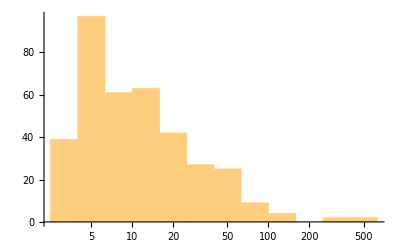

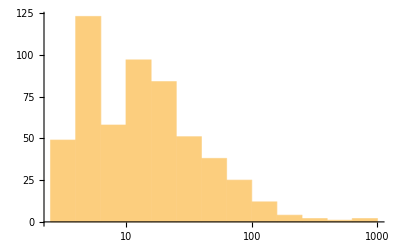

```mathematica
Histogram[Length/@gdat1,"Log"]
Histogram[Length/@gdat2,"Log"]
```

```mathematica
sharedProteins=Intersection[gdat1[[All,1,2]],gdat2[[All,1,2]]];
gdat1=gdat1[[Table[Position[gdat1[[All,1,2]],sharedProteins[[i]]],{i,Length[sharedProteins]}]//Flatten]];
gdat2=gdat2[[Table[Position[gdat2[[All,1,2]],sharedProteins[[i]]],{i,Length[sharedProteins]}]//Flatten]];
```

```mathematica
labels=heads[[11;;18]];
α=0.5;
```

```mathematica
{quants1,quants2}=Table[Table[Association@Thread[labels->GeometricMean/@Transpose[Values@#⟦i,All,Key/@labels⟧+α]],{i,Length[#]}]&[j],{j,{gdat1,gdat2}}];
```

```mathematica
quants=Join[Values@quants1ᵀ,Values@quants2ᵀ]ᵀ;
```

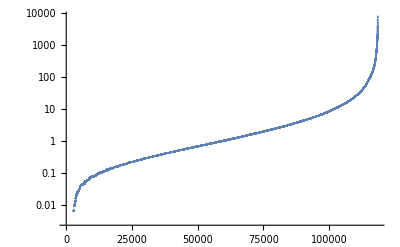

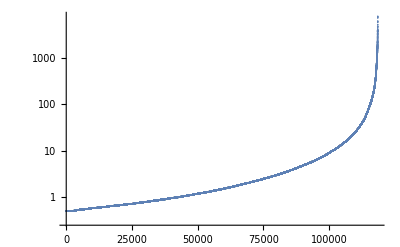

```mathematica
ListLogPlot[Sort[Flatten[Values@b2]],PlotRange->Full]
ListLogPlot[Sort[Flatten[Values@b2]]+α,PlotRange->Full]
```

### Cluster Analysis

#### Dendrograms

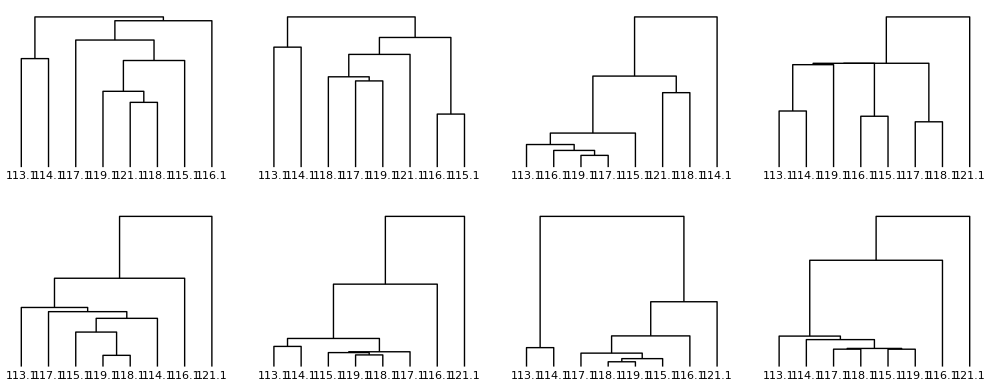

```mathematica
GraphicsGrid[{
{"","Unnormalised","Channel-sum correction","Median correction","Median corrected shared proteins"},
{"iTRAQ1",
DendrogramPlot[Values@c1ᵀ,LeafLabels->heads[[11;;18]]],
DendrogramPlot[Values@a1ᵀ,LeafLabels->heads[[11;;18]]],
DendrogramPlot[Values@b1ᵀ,LeafLabels->heads[[11;;18]]],
DendrogramPlot[Values@quants1ᵀ,LeafLabels->heads[[11;;18]]]
},
{"iTRAQ2",
DendrogramPlot[Values@c2ᵀ,LeafLabels->heads[[11;;18]]],
DendrogramPlot[Values@a2ᵀ,LeafLabels->heads[[11;;18]]],
DendrogramPlot[Values@b2ᵀ,LeafLabels->heads[[11;;18]]],
DendrogramPlot[Values@quants2ᵀ,LeafLabels->heads[[11;;18]]]
}}]
```

#### PCA plots

```mathematica
pca1a=PrincipalComponents[Values@a1ᵀ];
pca1b=PrincipalComponents[Values@b1ᵀ];
pca1c=PrincipalComponents[Values@quants1ᵀ];
pca2a=PrincipalComponents[Values@a2ᵀ];
pca2b=PrincipalComponents[Values@b2ᵀ];
pca2c=PrincipalComponents[Values@quants2ᵀ];
```

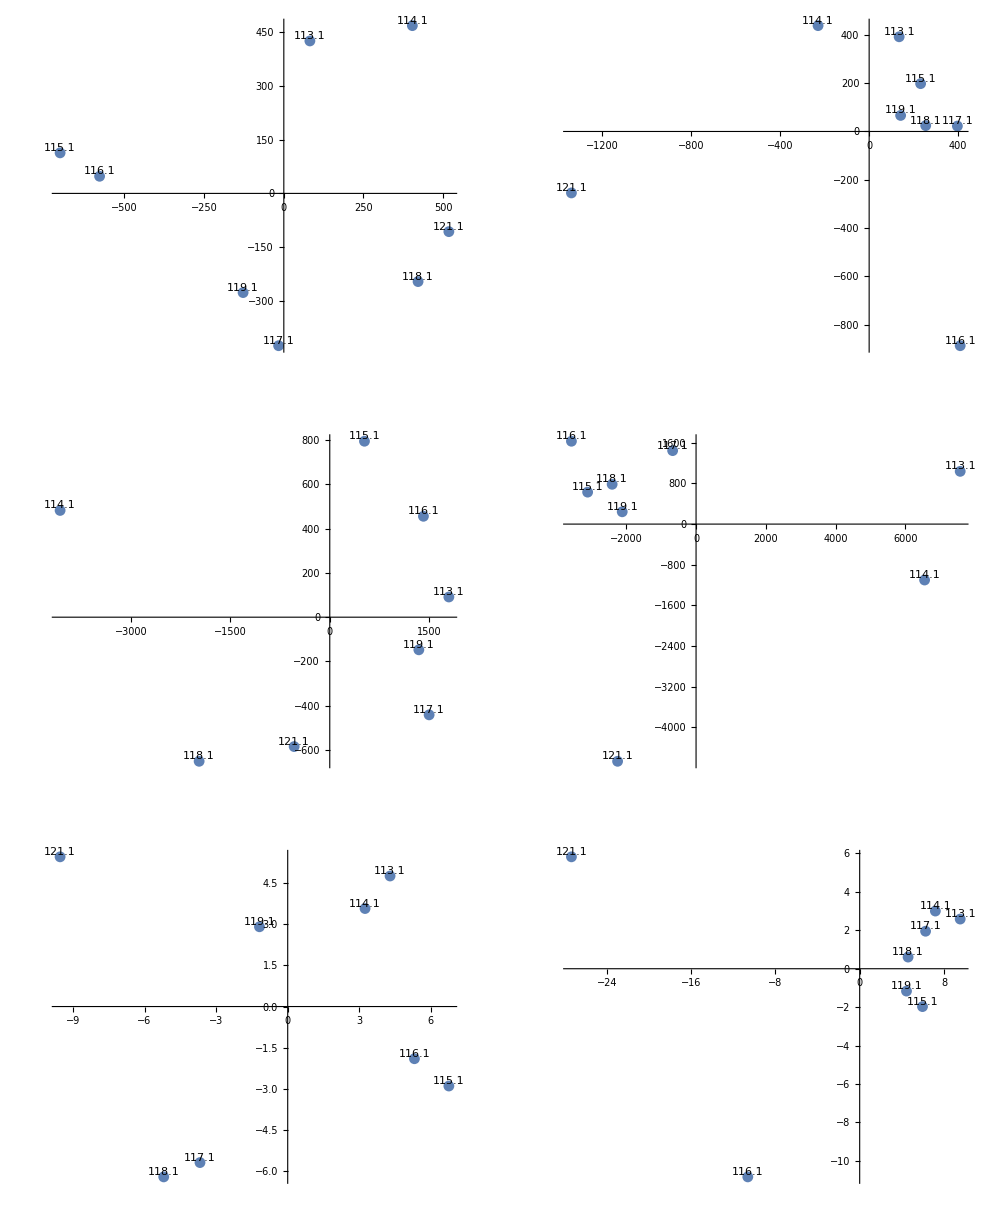

```mathematica
GraphicsGrid[{{"","iTRAQ1","iTRAQ2"},
{"ChannelSum",pcaPlot1a=ListPlot[pca1a[[All,1;;2]],Epilog->Table[Text[heads[[11;;18]][[i]],pca1a[[i,{1,2}]],{0,-2}],{i,8}],PlotRangePadding->Scaled[.1]],
pcaPlot2a=ListPlot[pca2a[[All,1;;2]],Epilog->Table[Text[heads[[11;;18]][[i]],pca2a[[i,{1,2}]],{0,-2}],{i,8}],PlotRangePadding->Scaled[.1]]},
{"Median Corrected",pcaPlot1b=ListPlot[pca1b[[All,1;;2]],Epilog->Table[Text[heads[[11;;18]][[i]],pca1b[[i,{1,2}]],{0,-2}],{i,8}],PlotRangePadding->Scaled[.1]],
pcaPlot2b=ListPlot[pca2b[[All,1;;2]],Epilog->Table[Text[heads[[11;;18]][[i]],pca2b[[i,{1,2}]],{0,-2}],{i,8}],PlotRangePadding->Scaled[.1]]},
{"Shared Median Correct",pcaPlot1c=ListPlot[pca1c[[All,1;;2]],Epilog->Table[Text[heads[[11;;18]][[i]],pca1c[[i,{1,2}]],{0,-2}],{i,8}],PlotRangePadding->Scaled[.1]],
pcaPlot2c=ListPlot[pca2c[[All,1;;2]],Epilog->Table[Text[heads[[11;;18]][[i]],pca2c[[i,{1,2}]],{0,-2}],{i,8}],PlotRangePadding->Scaled[.1],PlotRange->Full]}
}]
```

### Comparison of protein expression (Ratios)

```mathematica
labs={"aWT","aWT2","a15G","a15G","a16G","a16G","a15_blank","a15_blank","bWT","bWT2","b5G","b5G","b8G","b8G","b10G","b10G"}
```

{aWT,aWT2,a15G,a15G,a16G,a16G,a15_blank,a15_blank,bWT,bWT2,b5G,b5G,b8G,b8G,b10G,b10G}

```mathematica
{ratio1,ratio2}={Table[Values@quants1[[i]]/Mean[Values@quants1[[i,1;;2]]],{i,Length[quants1]}],Table[Values@quants2[[i]]/Mean[Values@quants2[[i,1;;2]]],{i,Length[quants2]}]};
```

Comparison of 113 114 from iTRAQ1 and 2 after ratio division. They are consistently reflective of each other (seen by checkerboard effect).

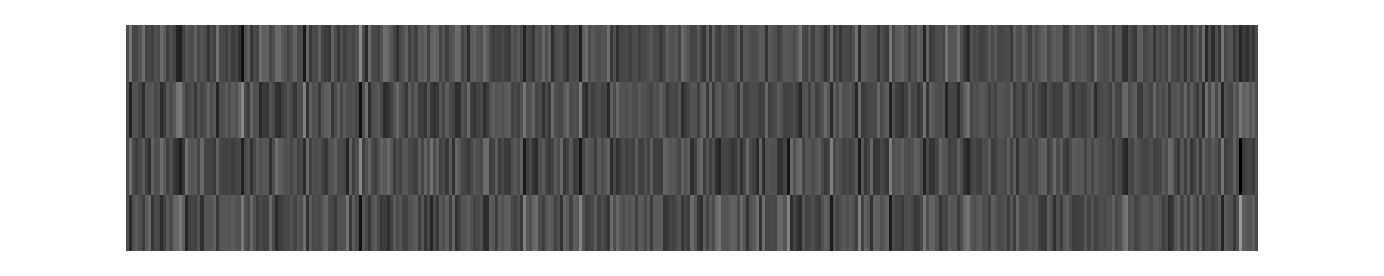

```mathematica
ArrayPlot[Join[
ratio1[[All,1;;2]]ᵀ,
ratio2[[All,1;;2]]ᵀ]
]
```

```mathematica
labs
```

{aWT,aWT2,a15G,a15G,a16G,a16G,a15_blank,a15_blank,bWT,bWT2,b5G,b5G,b8G,b8G,b10G,b10G}

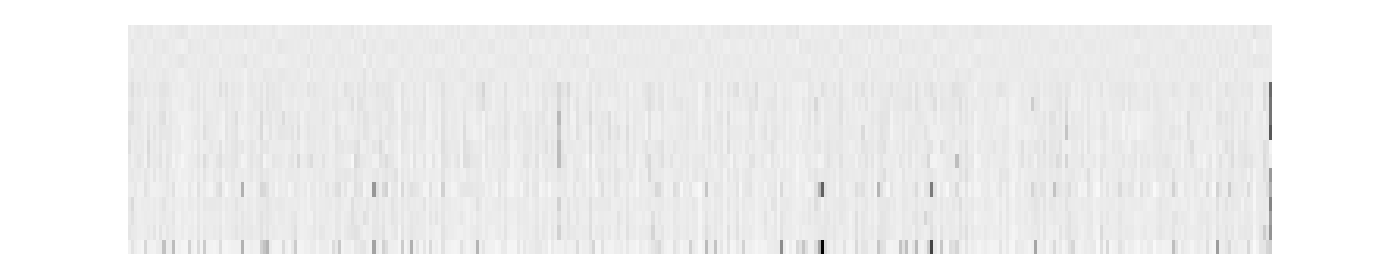

```mathematica
ArrayPlot[Join[
ratio2[[All,1;;2]]ᵀ,
ratio1[[All,All]]ᵀ,
ratio2[[All,3;;8]]ᵀ]
]
```

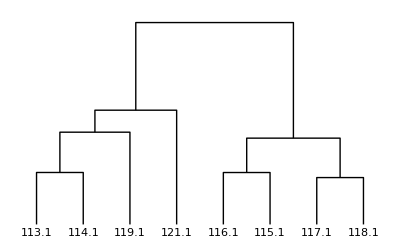

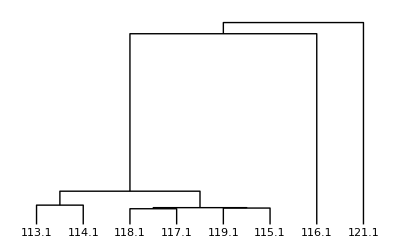

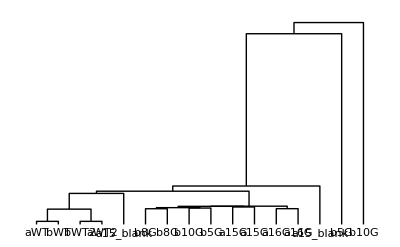

```mathematica
DendrogramPlot[ratio1ᵀ,LeafLabels->heads[[11;;18]]]
DendrogramPlot[ratio2ᵀ,LeafLabels->heads[[11;;18]]]
DendrogramPlot[Join[ratio1ᵀ,ratio2ᵀ],LeafLabels->labs]
```

```mathematica
pcaRatio=PrincipalComponents[Join[ratio1ᵀ,ratio2ᵀ]];
```

```mathematica
pcaprots=PrincipalComponents[Join[ratio1ᵀ,ratio2ᵀ]ᵀ];
```

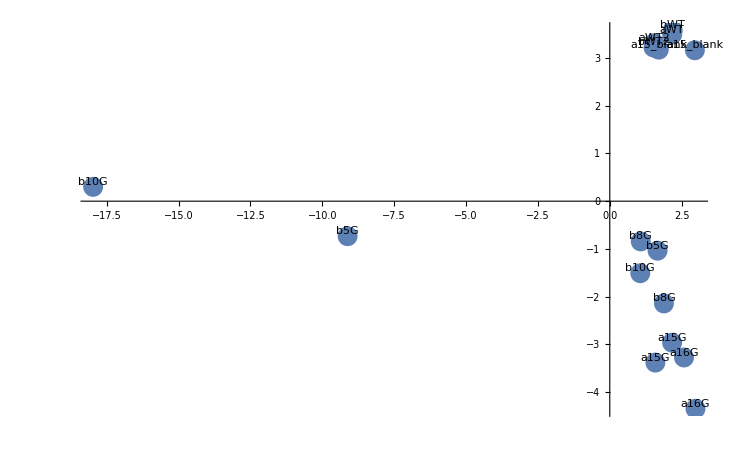

```mathematica
pcaPlotRatio=ListPlot[pcaRatio[[All,1;;2]],Epilog->Table[Text[labs[[i]],pcaRatio[[i,{1,2}]],{0,-2}],{i,16}],PlotRangePadding->Scaled[.1],PlotRange->Full]
```

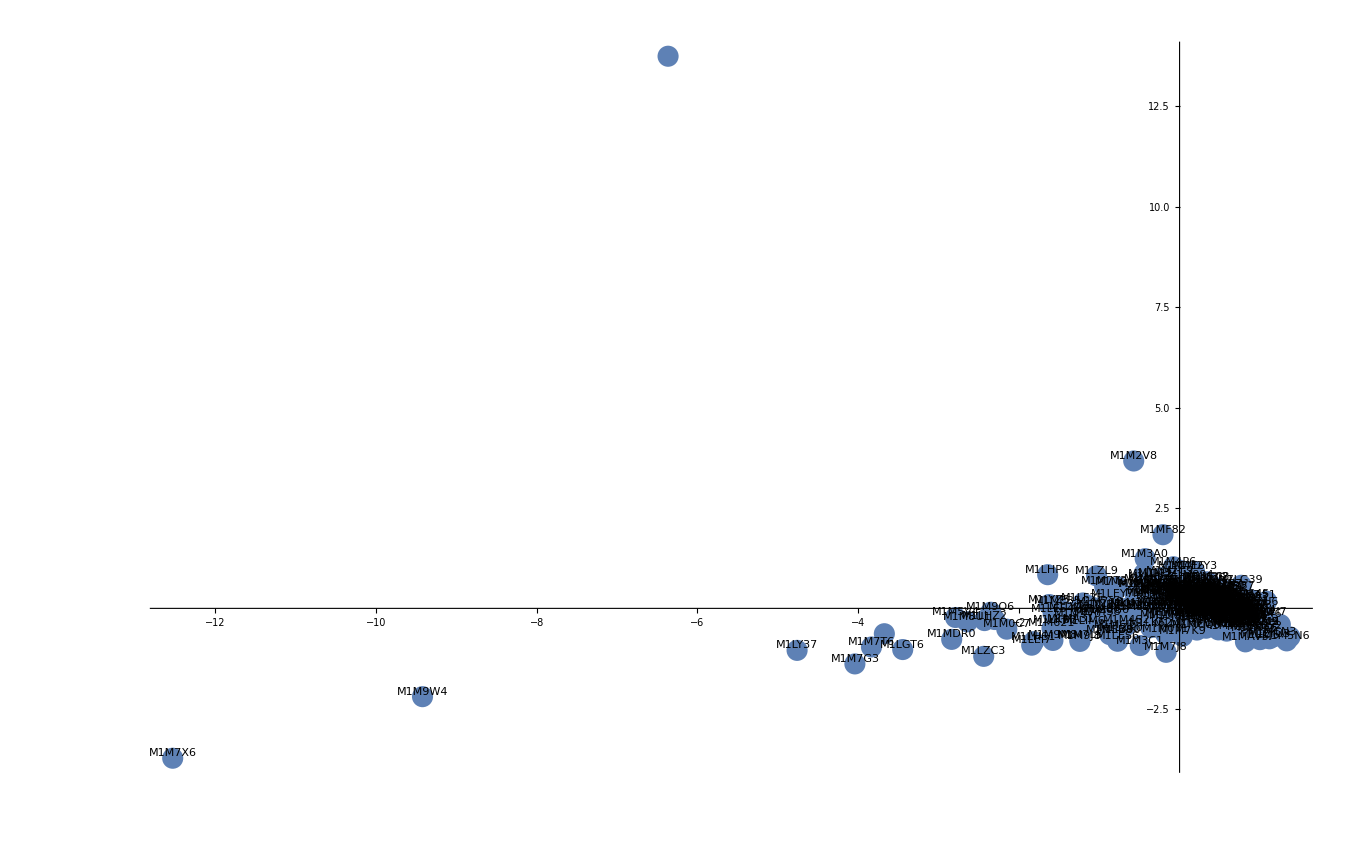

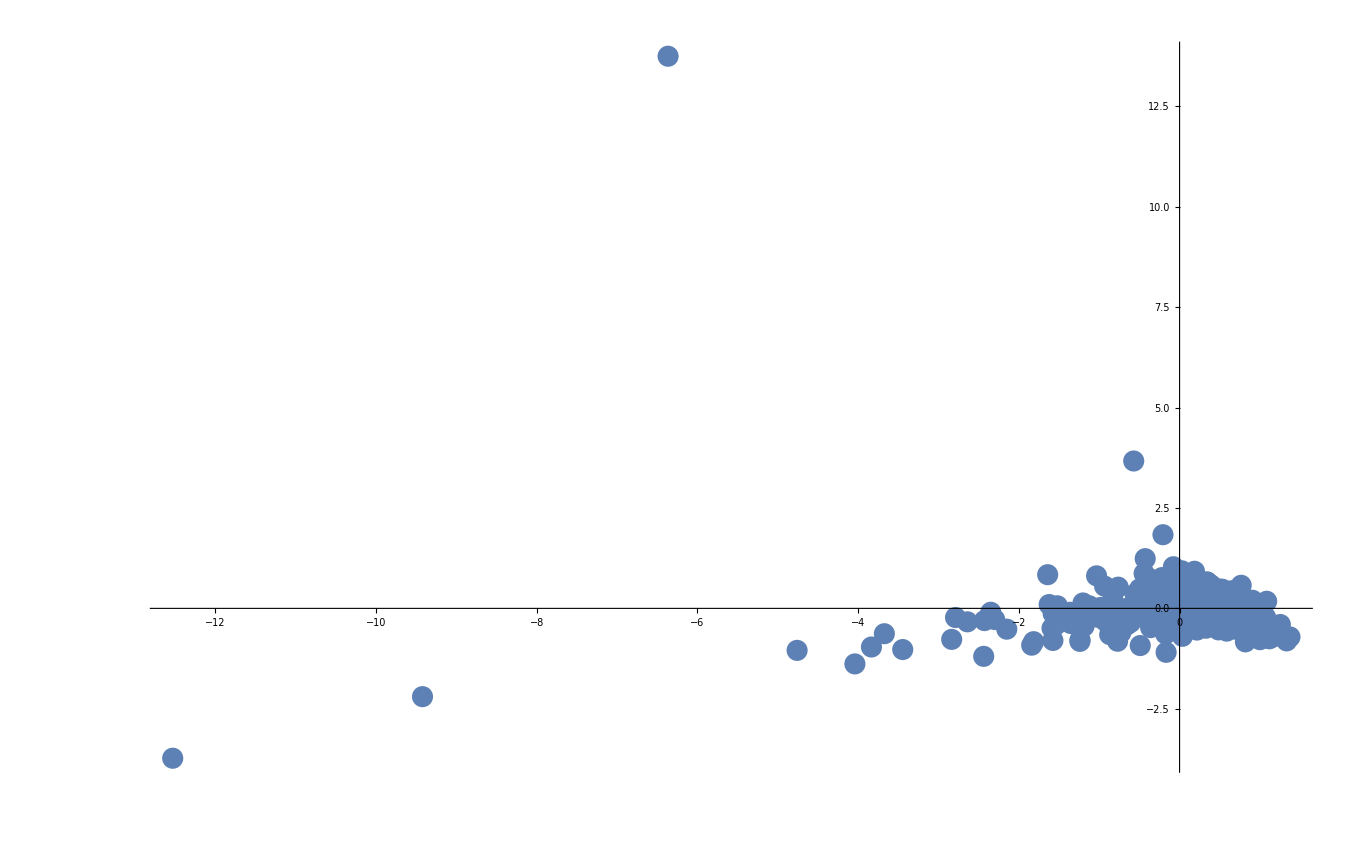

```mathematica
pcaPlotRatio=ListPlot[pcaprots[[All,1;;2]],Epilog->Table[Text[sharedProteins[[i]],pcaprots[[i,{1,2}]],{0,-2}],{i,Length[sharedProteins]}],PlotRangePadding->Scaled[.1],PlotRange->Full]
pcaPlotRatio=ListPlot[pcaprots[[All,1;;2]],Epilog->PlotRangePadding->Scaled[.1],PlotRange->Full]
```

```mathematica
a={labs,Join[ratio1ᵀ,ratio2ᵀ]ᵀ[[-1]],Exp[Join[ratio1ᵀ,ratio2ᵀ]ᵀ[[-1]]]};
```

```mathematica
a[[All,1;;8]]//TableForm
a[[All,9;;16]]//TableForm
```

aWT | aWT2 | a15G | a15G | a16G | a16G | a15_blank | a15_blank
1.00393 | 0.996067 | 7.28006 | 6.80283 | 6.77149 | 8.11185 | 0.556368 | 0.866531
2.72899 | 2.70761 | 1451.07 | 900.393 | 872.612 | 3333.73 | 1.74433 | 2.37864

bWT | bWT2 | b5G | b5G | b8G | b8G | b10G | b10G
0.98286 | 1.01714 | 5.01068 | 3.9141 | 5.99852 | 4.63505 | 5.25372 | 2.30489
2.67209 | 2.76528 | 150.007 | 50.104 | 402.832 | 103.033 | 191.276 | 10.0231

```mathematica
quants//Dimensions
```

{365,16}

```mathematica
labs
```

{aWT,aWT2,a15G,a15G,a16G,a16G,a15_blank,a15_blank,bWT,bWT2,b5G,b5G,b8G,b8G,b10G,b10G}

```mathematica
ratios=Join[ratio1ᵀ,ratio2ᵀ]ᵀ;
```

```mathematica
exportQuants=Insert[ratiosᵀ,Flatten[{sharedProteins}ᵀ],1]ᵀ;
exportQuants=Insert[exportQuants,Flatten[{"Protein",labs}],1];
Dimensions[exportQuants]
```

{366,17}

```mathematica
exportQuants[[1;;10,All]]//TableForm
```

Protein | aWT | aWT2 | a15G | a15G | a16G | a16G | a15_blank | a15_blank | bWT | bWT2 | b5G | b5G | b8G | b8G | b10G | b10G
M1LCZ5 | 0.994822 | 1.00518 | 1.19618 | 1.08813 | 1.47946 | 1.28534 | 1.55064 | 1.13041 | 1.01247 | 0.987528 | 1.05579 | 0.943242 | 1.19625 | 1.13218 | 1.25305 | 0.68498
M1LD32 | 0.763559 | 1.23644 | 1.59902 | 1.3377 | 1.51529 | 1.02822 | 0.938002 | 0.814016 | 0.807018 | 1.19298 | 1.15922 | 0.900402 | 1.77845 | 1.45934 | 1.08414 | 1.36968
M1LD57 | 1.03563 | 0.96437 | 1.08335 | 1.04569 | 1.05056 | 1.007 | 1.10661 | 1.06932 | 1.01247 | 0.987534 | 0.981505 | 1.11902 | 0.93825 | 1.00233 | 1.00158 | 0.889749
M1LD65 | 1.04044 | 0.959555 | 1.27203 | 1.08989 | 1.16546 | 1.12939 | 1.01275 | 1.30894 | 1.0968 | 0.903202 | 1.01527 | 0.721285 | 0.848564 | 0.807834 | 0.892635 | 0.617073
M1LD69 | 0.953992 | 1.04601 | 0.959745 | 1.08991 | 0.926452 | 1.04608 | 1.11911 | 1.08281 | 1.01602 | 0.98398 | 0.8807 | 0.731455 | 0.953231 | 0.858348 | 0.815462 | 0.483145
M1LD90 | 0.814195 | 1.18581 | 1.15107 | 0.71343 | 0.812997 | 0.757597 | 0.790457 | 0.636448 | 0.916111 | 1.08389 | 1.23163 | 1.43216 | 0.937412 | 0.954039 | 0.925186 | 1.94705
M1LDC2 | 1.05313 | 0.946867 | 1.05528 | 1.04488 | 1.26033 | 1.45338 | 1.85776 | 1.66988 | 1.07613 | 0.923867 | 1.02501 | 1.0625 | 0.957497 | 0.940847 | 1.12751 | 0.70725
M1LDD8 | 1.02084 | 0.979162 | 0.985853 | 0.90531 | 0.964692 | 0.894475 | 0.991305 | 0.960672 | 1.15841 | 0.841587 | 0.800655 | 0.727049 | 0.885431 | 0.929213 | 0.930375 | 0.695081
M1LDE0 | 1.06411 | 0.93589 | 1.11728 | 1.05256 | 0.99424 | 1.33309 | 1.12449 | 1.11852 | 0.878329 | 1.12167 | 1.24791 | 0.713134 | 1.04621 | 1.02448 | 1.32795 | 0.612847

```mathematica
Export["exportQuants.csv",exportQuants]
```

exportQuants.csv

{,aWT,aWT2,a15G,a15G,a16G,a16G,a15_blank,a15_blank,bWT,bWT2,b5G,b5G,b8G,b8G,b10G,b10G}

```mathematica
Join[{labs},quants][[1;;3]]
```

{{aWT,aWT2,a15G,a15G,a16G,a16G,a15_blank,a15_blank,bWT,bWT2,b5G,b5G,b8G,b8G,b10G,b10G},{6.1055,6.16905,7.34126,6.67815,9.07987,7.88849,9.51672,6.93762,2.51898,2.45692,2.62675,2.34674,2.97622,2.81681,3.11752,1.7042},{1.46058,2.36513,3.0587,2.55882,2.89853,1.96683,1.79426,1.5571,1.25857,1.86049,1.80784,1.40421,2.77356,2.27588,1.69075,2.13607}}